```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];SetOptions[$FrontEndSession,NotebookAutoSave->True];
NotebookSave[];
AppendTo[$Path,FileNameJoin[{$HomeDirectory,"Dropbox","EpidCRNmodels"}]];
<<EpidCRN`;<<red`;
var={E,LQ,LF0,LF1,LF2,LF3,NQ0,NQ1,NQ2,NQ3,NF0,NF1,NF2,NF3,A0,A1,A2,A3,M0,M1,M2,M3};
cT={M->M0+M1+M2+M3,
LF->LF0+LF1+LF2+LF3,
NF->NF0+NF1+NF2+NF3,
A->A0+A1+A2+A3};

RH={(*E-Eggs*)bE*A-(muE+dE)*E,(*LQ-Questing larvae*)dE*E-(muLQ+fL)*LQ,(*LF0-3-Feeding larvae*)fL*LQ-(dL+muLF+DL*LF)*LF0-((be11*M1+be31*M3+be22*M2+be32*M3+be33*M3)*fL*LQ)/M,((be11*M1+be31*M3)*fL*LQ)/M-(dL+muLF+DL*LF)*LF1,((be22*M2+be32*M3)*fL*LQ)/M-(dL+muLF+DL*LF)*LF2,(be33*M3*fL*LQ)/M-(dL+muLF+DL*LF)*LF3,(*NQ0-3-Questing nymphs*)dL*LF0-(muNQ+fN)*NQ0,dL*LF1-(muNQ+fN)*NQ1,dL*LF2-(muNQ+fN)*NQ2,dL*LF3-(muNQ+fN)*NQ3,(*NF0-3-Feeding nymphs*)fN*NQ0-(dN+muNF+DN*NF)*NF0-((beb11*M1+beb31*M3+beb22*M2+beb32*M3+beb33*M3)*fN*NQ0)/M,fN*NQ1-(dN+muNF+DN*NF)*NF1+((beb11*M1+beb31*M3)*NQ0-beNQ123*NQ1*M2-beNQ133*NQ1*M3)*fN/M,fN*NQ2-(dN+muNF+DN*NF)*NF2+((beb22*M2+beb32*M3)*NQ0-beNQ213*NQ2*M1-beNQ233*NQ2*M3)*fN/M,fN*NQ3-(dN+muNF+DN*NF)*NF3+(beNQ123*NQ1*M2+beNQ213*NQ2*M1+beNQ233*NQ2*M3+beb33*M3*NQ0+beNQ133*NQ1*M3)*fN/M,(*A0-3-Adults*)dN*NF0-muA*A0,dN*NF1-muA*A1,dN*NF2-muA*A2,dN*NF3-muA*A3,(*M0-3-Mice*)bM*M-(muM+DM*M)*M0-(fN*M0*(ga11*NQ1+ga31*NQ3+ga22*NQ2+ga32*NQ3+ga33*NQ3))/M,(fN*((ga11*NQ1+ga31*NQ3)*M0-(gab23*NQ2+gab33*NQ3)*M1))/M-(muM+DM*M)*M1,(fN*((ga22*NQ2+ga32*NQ3)*M0-(gat13*NQ1+gat33*NQ3)*M2))/M-(muM+DM*M)*M2,(fN*(ga33*NQ3*M0+(gab23*NQ2+gab33*NQ3)*M1+(gat13*NQ1+gat33*NQ3)*M2))/M-(muM+DM*M)*M3};RHS=RH//.cT;
{RN,rts,spe,alp,bet,gam}=ODE2RN[RHS,var];
RHS-gam.rts//FullSimplify  (*Should be {0,0,0,0}*)
mSi= minSiph[spe, RN][[1]];
Print["minSiph=", mSi];
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

$Aborted

minSiph=mSi

{0,0,0,0}

minSiph={{i1,i12},{i2,i12}}{{i1,i12},{i2,i12}}

14 reactions and transitions: (0→s | mu0 s0
i12+s→i1+i12 | be1 i12 s
i1+s→2 i1 | (i1 mu1 R1 s)/s0
i12+s→i12+i2 | be2 i12 s
i2+s→2 i2 | (i2 mu2 R2 s)/s0
i1+i12→2 i12 | et1 i1 i12
i1+i2→i12+i2 | ga1 i1 i2
i1+i2→i1+i12 | ga2 i1 i2
i12+i2→2 i12 | et2 i12 i2
i12+s→2 i12 | (i12 mu3 R3 s)/s0
s→0 | mu0 s
i1→0 | i1 mu1
i2→0 | i2 mu2
i12→0 | i12 mu3)

RHS=(-(((be1+be2) i12+mu0) s)-((i1 mu1 R1+i2 mu2 R2+i12 mu3 R3) s)/s0+mu0 s0
-i1 (et1 i12+ga1 i2+mu1)+be1 i12 s+(i1 mu1 R1 s)/s0
-i2 (ga2 i1+et2 i12+mu2)+be2 i12 s+(i2 mu2 R2 s)/s0
et1 i1 i12+ga1 i1 i2+ga2 i1 i2+et2 i12 i2-i12 mu3+(i12 mu3 R3 s)/s0) siphons are{{i1,i12},{i2,i12}}((R1 s)/s0 | (be1 s)/mu3 | 0
0 | (R3 s)/s0 | 0
0 | (be2 s)/mu3 | (R2 s)/s0)

reduced models are{{s},{i1},{i2},{i12}}

Minimal siphons: {T_1→{i1,i12},T_2→{i2,i12}}

IGMS edges: {1->2,2->1}

Cycles found: 1

Cycles: {{1->2,2->1}}

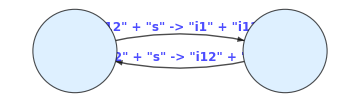

{{i12},{i1},{i2}}

```mathematica
{RHS,var,par,cp,mSi,Jx,Jy,cDFE,E0,K,R0A,infVars,ng}=bdAn[RN,rts,var];
Print[RN//Length, " reactions and transitions: ",Transpose[{RN,rts}]//MatrixForm]
Print["RHS=",RHS//FullSimplify//MatrixForm, " siphons are",mSi,K//MatrixForm];
(* MAXIMAL ELIMINABLE SETS *)
{maxId, maxSets} = maxElim[RN, rts, var];
Print["reduced models are",maxSets];
{edg,elab,cyc,graph}=IGMS[RN, mSi];
{co,nc}=findCores[RN,3];co
```

10reactions and transitions: (0→s | mu0 s0
i1+s→2 i1 | (i1 mu1 R1 s)/s0
i2+s→2 i2 | (i2 mu2 R2 s)/s0
i12+s→2 i12 | (i12 mu3 R3 s)/s0
i1+i12→2 i12 | et1 i1 i12
i12+i2→2 i12 | et2 i12 i2
s→0 | mu0 s
i1→0 | i1 mu1
i2→0 | i2 mu2
i12→0 | i12 mu3)

RHS=(-(i1 mu1 R1 s+i2 mu2 R2 s+i12 mu3 R3 s+mu0 s s0-mu0 s0^2)/s0
-i1 (et1 i12+mu1)+(i1 mu1 R1 s)/s0
-i2 (et2 i12+mu2)+(i2 mu2 R2 s)/s0
i12 (et1 i1+et2 i2+mu3 (-1+(R3 s)/s0)))mSi={{i1},{i2},{i12}}

al,be arealbe  DFE is{s→s0,i1→0,i12→0,i2→0} repr. functions  {(R1 s)/s0,(R2 s)/s0,(R3 s)/s0}

K=((R1 s)/s0 | 0 | 0
0 | (R3 s)/s0 | 0
0 | 0 | (R2 s)/s0)F=((mu1 R1 s)/s0 | 0 | 0
0 | (mu3 R3 s)/s0 | 0
0 | 0 | (mu2 R2 s)/s0)V=(et1 i12+mu1 | et1 i1 | 0
-et1 i12 | -et1 i1-et2 i2+mu3 | -et2 i12
0 | et2 i2 | et2 i12+mu2)

Minimal siphons: {T_1→{i1},T_2→{i2},T_3→{i12}}

IGMS edges: {1->3,2->3}

IGMS is acyclic

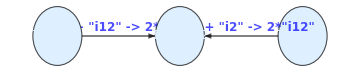

```mathematica
(*part. case*)RNbg={0->"s","s"+"i1"->2*"i1","s"+"i2"->2*"i2","s"+"i12"->2*"i12","i1"+"i12"->2*"i12","i2"+"i12"->2*"i12","s"->0,"i1"->0,"i2"->0,"i12"->0};
rtsbg={s0 mu0,mu1 s0^(-1)  *R1*s*i1,mu2  s0^(-1)  *R2*s*i2,mu3  s0^(-1)  *R3*s*i12,et1*i1*i12,et2*i2*i12,mu0*s,mu1*i1,mu2*i2,mu3*i12};
Print[RNbg//Length,"reactions and transitions: ",Transpose[{RNbg,rtsbg}]//MatrixForm]
{RHS,var,par,cp,mSi,Jx,Jy,cDFE,E0,K,R0A,infVars,ng}= bdAn[RNbg,rtsbg,var];
Print["RHS=",RHS//FullSimplify//MatrixForm,"mSi=",mSi];

F=ng[[2]];V=ng[[3]];
Print["al,be are",al//MatrixForm,be//MatrixForm,"  DFE is",E0," repr. functions  ",R0A];
Print["K=",K//MatrixForm,"F=",F//MatrixForm,"V=",V//MatrixForm];
{edg,elab,cyc,graph}=IGMS[RNbg, mSi];
```

```mathematica
s1=1/R1;
s2=1/R2;s3=1/R3;s13=s0/(1+mu1 mu3 (1/s1-1/s3)/(et1  mu0));
s23=s0/(1+mu2 mu3 (1/s2-1/s3)/(et2 mu0));con=And@@cp&&s0>s3>s23>s2&&s3>s13>s1;
fi=FindInstance[con,par][[1]];
RHSc1=RHS/.c1;
cN=Union[cmu,cbg,(cb/.cmu),(fi/.cmu)]
(*3D phase portrait using phase3 with improved options*)
rhN3D=RHSc1[[{1,3,4}]]//.cN;
(*Variables[rhN3D]={s,i2,i12}*)
{fp3,eig3,stab3,pFP3,pStream3}=phase3[rhN3D,50,12,0.01,StreamScale->0.05];
Show[pFP3,pStream3,PlotLabel->"3D: i1=0 face (s,i2,i12)",ImageSize->Large,ViewPoint->{1.5,-2,1.5}]
```

{b→mu s0,be1→0,be2→0,et1→5/8,et2→5/8,ga1→0,ga2→0,mu→1,mu0→mu,mu1→mu,mu2→mu,mu3→mu,R1→2,R2→2,R3→1,s0→2}

fp={{0.,0.,2.},{0.,1.,1.},{0.177778,0.711111,1.11111}} eig={{1.,-1.,0},{-1.,0.25+0.25 ⅈ,0.25-0.25 ⅈ},{-1.,0.666667,-0.133333}} stab={Saddle,Saddle,Saddle}

Show::gcomb: Could not combine the graphics objects in Show[,«3»,ViewPoint→{1.5,-2,1.5}].

Show[-Graphics3D-,StreamPlot3D[{2-s-(i12 s)/2-i2 s,-i2-(5 i12 i2)/8+i2 s,-i12+(5 i12 i2)/8+(i12 s)/2},EpidCRN`Private`r1$245474,EpidCRN`Private`r2$245474,EpidCRN`Private`r3$245474,StreamMarkers→Arrow3D,StreamStyle→Directive[Opacity[0.7],Thickness[0.005]],StreamColorFunction→Rainbow,StreamPoints→12,BoxRatios→{1,1,1},AxesLabel→ToString/@EpidCRN`Private`var$245474,StreamScale→0.05],PlotLabel→3D: i1=0 face (s,i2,i12),ImageSize→Large,ViewPoint→{1.5,-2,1.5}]

```mathematica
Show[pFP3,pStream3,PlotLabel->"3D: Siphon face i1=0 (s,i2,i12)",ImageSize->Large,ViewPoint->{1.5,-2,1.5}]
```

{b→mu s0,be1→0,be2→0,et1→5/8,et2→5/8,ga1→0,ga2→0,mu→1,mu0→mu,mu1→mu,mu2→mu,mu3→mu,R1→2,R2→2,R3→1,s0→2}

Error: phase3 requires 3D system, got 4D

-Graphics3D-